# Équation de Helmholtz III

((Les conditions frontières:ⅆ/ⅆx X[x]|)_(x=0) , ⅆ/ⅆx X[x]|)_(x=L)

## Équation d^2/dx^2 X(x)+k^2 X(x)=0

### La longueur

```mathematica
L:=2
```

### La phase initiale

```mathematica
α:=π/2
```

### Les valeurs propres

```mathematica
Subscript[k, n_]:=(n π)/L
```

```mathematica
Table[Subscript[k, n],{n,1,6}]
```

{π/2,π,(3 π)/2,2 π,(5 π)/2,3 π}

### Les fonctions propres

```mathematica
Subscript[X, n_][x_]=√(2/L)Sin[Subscript[k, n]  x+α]
```

Cos[(n π x)/2]

```mathematica
Table[Subscript[X, n][x],{n,1,6}]
```

{Cos[(π x)/2],Cos[π x],Cos[(3 π x)/2],Cos[2 π x],Cos[(5 π x)/2],Cos[3 π x]}

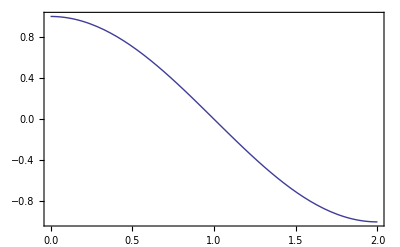
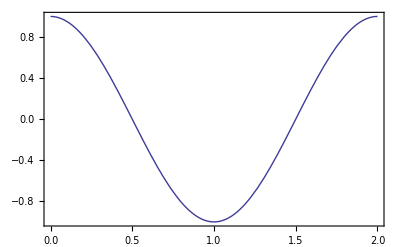
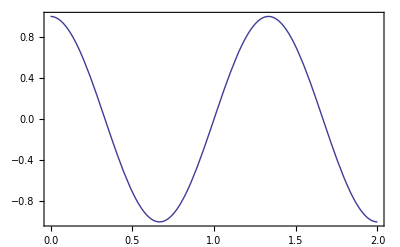
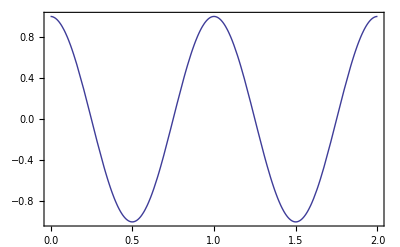
1 | π/2 | Cos[(π x)/2] | -Graphics-
2 | π | Cos[π x] | -Graphics-
3 | (3 π)/2 | Cos[(3 π x)/2] | -Graphics-
4 | 2 π | Cos[2 π x] | -Graphics-

```mathematica
Table[{n,Subscript[k, n],Subscript[X, n][x],Plot[Subscript[X, n][x],{x,0,L},Frame->True]},{n,1,4}]//TableForm
```

### Solution Général

```mathematica
X[x_]=∑_(n=1)^6 Subscript[X, n][x]
```

Cos[(π x)/2]+Cos[π x]+Cos[(3 π x)/2]+Cos[2 π x]+Cos[(5 π x)/2]+Cos[3 π x]

```mathematica
Manipulate[∑_(n=1)^N Subscript[X, n][x],{N,1,20,1}]
```

```mathematica
Manipulate[Plot[∑_(n=1)^N Subscript[X, n][x],{x,0,L},AxesLabel->{"x","X(x)"},PlotLabel->Style[With[{N=N},HoldForm[X[x]=∑_(n=1)^N Subscript[X, n][x]]],12],PlotRange->{-2,15}],{N,1,20,1}]
```